```mathematica
<<KirillBelov`WebSocketLink`
```

```mathematica
connection = WebSocketConnect["wss://stream.binance.com:9443/ws/btcusdt@miniTicker"];
```

```mathematica
Block[{isOpen}, connection["Client"] @ isOpen[]]
```

True

```mathematica
connection["Data"]["Elements"]
```

```mathematica
ltpClient = Block[{ltpClient}, connection["Client"] @ ltpClient]
```

«JavaObject[kirillbelov.websocketlink.LTPClient]»

```mathematica
Block[{redirectPort, redirectHost, redirectSocket}, 
ltpClient /@ {redirectPort, redirectHost, redirectSocket}
]
```

{23192,localhost,«JavaObject[java.net.Socket]»}

```mathematica
handler = connection["Listener"]["Handler"]["Handler"]
```

<||>

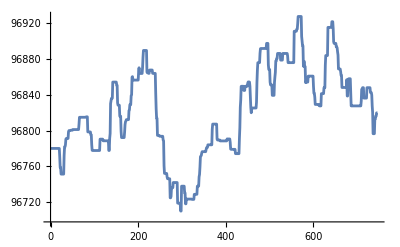

```mathematica
ListLinePlot[ToExpression /@ connection["Data"]["Elements"][[All, "c"]]]
```